```mathematica
(*Energy/Nutrient Density*)
lightDensity = 10;
nutrientDensity = 8;
(*Plant efficiencies and costs*)
(*Light Absorbtion Efficiency*)
lightEfficiency = 0.7;
(*Stem Energy Costs*)
hECost = 3.5;
wECost = 1.5;
lECost=0.75;
(*Root Energy Costs*)
rwECost = 1.5;
rECost = 1.0;
(*Stem Nutrient Costs*)
hNCost = 3.5;
wNCost = 1.25;
lNCost = 1.;
(*Root Nutrient Costs*)
rwNCost = 1.;
rNCost = 0.5;
(*Plant Max*)
maxHeight =10;
maxWidth = 0.5;
maxLeaves = 1.;
maxRWidth = 0.5;
maxRSize = 1.;
```

```mathematica
(*Plant Functions*)
```

```mathematica
Height := f*maxHeight;
Width:= f*maxWidth;
Leaves := f*maxLeaves;
RWidth := f*maxRWidth;
RSize := f*maxRSize;
sunArea := Pi*Width^2
EnergyMaintainance := Height*hECost + Width^2*wECost + Leaves^1.5*lECost
EnergyBudget := sunArea*lightDensity*Leaves*lightEfficiency;
NutrientMaintainance :=Height*hNCost + Width^2*wNCost + Leaves^1.5*lNCost
```

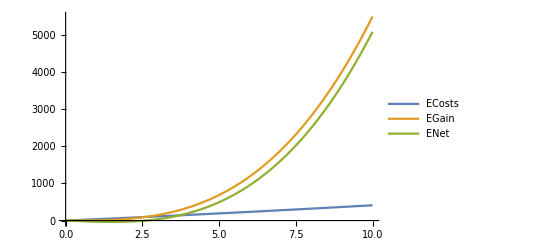

```mathematica
Plot[{EnergyMaintainance, EnergyBudget, EnergyBudget-EnergyMaintainance},{f,0,10},PlotLegends->{"ECosts", "EGain", "ENet"}]
```

```mathematica
Energy
Nutrient
```

5. f+0.1 f^1.5+0.0625 f^2

5. f+0.1 f^1.5+0.0625 f^2